```mathematica
Code20[inp_]:=With[{a=BitShiftLeft[inp, 2], b=BitShiftLeft[inp, 1], c=inp, d=BitShiftRight[inp, 1], e=BitShiftRight[inp, 2]},BitXor[BitOr[a, b, c,d,e], BitXor[a,b,c,d,e]]]
```

```mathematica
Lifetime[inp_]:=Module[{seen=CreateDataStructure["HashSet", {0}], o=inp, count=0, gap=0, gapsum=0},
While[
seen["Insert",o]&&count<10000,
count++;
o=Code20[o];
gap=Max[gap, LargestGap[IntegerDigits[o, 2]]];
];
If[count==10000, 0,count]
]
Loss[inp_]:=Module[{seen=CreateDataStructure["HashSet", {0}], o=inp, count=0, gap=0},
While[
seen["Insert", o]&&count<10000,
count++;
o=Code20[o];
gap=Max[gap, LargestGap[IntegerDigits[o, 2]]];
];
If[count==10000, 0, -count+(gap/5)^4]
]
```

```mathematica
LargestGap[l_]:=Max[Length/@Select[Split[l],First[#]==0&],0]
LargestGap[{1,0,1,0,0,0,1,0,1,1,1,1}]
LargestGap[{0, 0, 0, 0, 0}]
LargestGap[{1,1, 1, 1, 1}]
```

3

5

0

```mathematica
rand=RandomInteger[{0, 1}, 100];
RepeatedTiming[LargestGap[rand]]
```

{0.0000241315,5}

```mathematica
l={1,0,0,0,1,0,1,1,1,1};
Lifetime[FromDigits[l, 2]];
ArrayPlot[CellularAutomaton[{20, {2, 1}, 2}, {l, 0}, %+5], ImageSize->Tiny]
```

-Graphics-

1

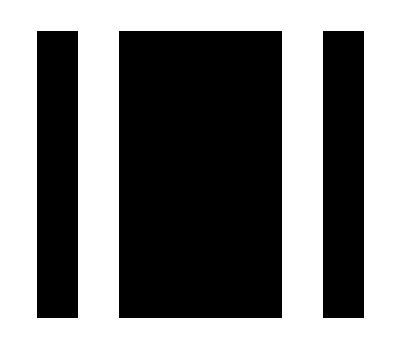

```mathematica
l={1, 0, 1, 1, 1, 1, 0, 1};
Lifetime[FromDigits[l, 2]]
ArrayPlot[CellularAutomaton[{20, {2, 1}, 2}, {l, 0}, %+5]]
```

```mathematica
l=RandomInteger[{0, 1}, 10];
Lifetime[FromDigits[l]]
ArrayPlot[CellularAutomaton[{20, {2, 1}, 2}, {l, 0}, %+5]]
```

60

-Graphics-

```mathematica
RandomFlip[inp_, n_]:=BitXor[inp, BitShiftLeft[1, RandomInteger[{0, n-1}]]]
RandomFlips[k_][inp_, n_]:=Nest[RandomFlip[#, n]&, inp, k]
```

```mathematica
ParallelSortBy[list_, func_]:=With[{cache=Association@ParallelTable[elem->func[elem], {elem, list}]}, SortBy[list, cache]]
```

```mathematica
RepeatedTiming[ParallelSortBy[Range[100], (Pause[0.01];#^2)&]]
```

{0.103566,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}}

```mathematica
GeneticOptimize[loss_, n_, numpoints_:100, minpoints_:10, steps_:100]:=Module[
{points=RandomInteger[{0, 2^n}, 100], stdout=PrintTemporary[""],minloss},

Do[
points=ParallelSortBy[points, loss];
minloss=loss[points[[1]]];
points=Join[points,Join@@ParallelTable[Table[RandomFlip[point, n], {i, Ceiling[numpoints/minpoints]}], {point, points[[;;minpoints]]}]][[;;numpoints]];
points=First/@GatherBy[points, Lifetime];
NotebookDelete[stdout];stdout=PrintTemporary["Step ",step, "/", steps, " | ", Length[points], " points with minimum loss ", minloss];,
{step, steps}];
points=ParallelSortBy[points, loss];
points[[1]]
]
```

```mathematica
Timing[l=GeneticOptimize[Loss,100, 100, 10, 100]]
```

{139.828,450159957124063884965837614235}

```mathematica
Timing[l=GeneticOptimize[Loss,1000, 500, 50, 1000]]
```

```mathematica
ll=IntegerDigits[l, 2]
Lifetime[l]
ArrayPlot[CellularAutomaton[{20, {2, 1}, 2}, {ll, 0}, If[%==0, 200,%+15]]]
```

{1,0,1,1,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,0,1,0,1,1,0,1,1,0,0,1,1,0,1,1,1,1,1,1,1,1,0,1,0,0,1,1,1,0,0,1,1,0,0,0,1,0,1,0,1,1,0,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,0,1,0,0,1,1,0,1,1}

61

-Graphics-

```mathematica
Iconize[l]
```